Read me

This notebook can be used to reproduce the results shown in Fig. 4 of “Online quantum time series processing with random oscillator networks” (https://arxiv.org/abs/2108.00698) in the manner described in the preprint. It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2 for Microsoft Windows (64-bit). 

To use it, evaluate Sections 1 and  2.1 first. The parameter “realizations” controls how many samples are used to generate the ensemble averages and is by default set to 10. In “Online quantum time series processing with random oscillator networks” a value of 100 has been used, but notice that this might take a while to finish.

Then you can proceed with either 2.2 or 2.3. Inside these subsections cells should in general be evaluated in order, i.e. plots can be made only after data has been generated and so on. Both need to be evaluated before 2.4 which simply combines the results into a single figure. 

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

Summary of the license
This work is licensed under CC BY 4.0. You are free to share and adapt the material as long as it remains under the same license  and you give appropriate credit. For the full legal text see LICENSE in the main repository.

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

Parallelization is used to speed up certain parts of the computations. We launch the maximum number of them now.

```mathematica
If[$ProcessorCount-$KernelCount>0,LaunchKernels[$ProcessorCount-$KernelCount]]
```

## User-defined functions

### Auxiliary

#### Permutations

```mathematica
(*permutes qqq..ppp.. to qpqpqp..*)
getmatP=Function[m,IdentityMatrix[2m,WorkingPrecision->MachinePrecision][[Riffle[Range[m],Range[m]+m]]]];
```

#### Plotting

These ones are for array and matrix plots you know.

```mathematica
getcoords=Function[{dim,index},Scaled[{(Last[index]-0.5)/Last[dim],1-(First[index]-0.5)/First[dim]}]];
```

```mathematica
getarraylabels=Function[{ar,sty},MapIndexed[Text[Style[#1,sty],getcoords[Dimensions[ar],#2]]&,ar,{2}]];
```

```mathematica
makearraylabels=Function[{ar,round,sty},Epilog->getarraylabels[Round[ar,round],sty]];
```

#### Graphs

```mathematica
Clear[completegraphrandomweights];
completegraphrandomweights[n_]:=SetProperty[CompleteGraph[n],EdgeWeight->{_:>RandomReal[{0.,2.}]}];
```

```mathematica
Clear[weightedKirchhoffMatrix];
weightedKirchhoffMatrix[g_]:=DiagonalMatrix[Tr/@Transpose@#]-#&@WeightedAdjacencyMatrix[g]
```

### State related

#### Multimode state generator

```mathematica
(*random symplectic matrix, qqq..ppp.. ordering*)
getrandommatS=Function[{m,rmin,rmax},With[{matU1=RandomVariate[CircularUnitaryMatrixDistribution[m]],matU2=RandomVariate[CircularUnitaryMatrixDistribution[m]],listr=RandomReal[{rmin,rmax},m]},
ArrayFlatten[{{Re[matU1],Im[matU1]},{-Im[matU1],Re[matU1]}}].DiagonalMatrix[Exp[listr]~Join~Exp[-listr]].ArrayFlatten[{{Re[matU2],Im[matU2]},{-Im[matU2],Re[matU2]}}]
]
];
```

```mathematica
(*random covariance matrix of m resonant QHOs in single mode thermal states, qqq..ppp.. ordering*)
getrandomσth=Function[{m,nthmin,nthmax,ωbare},With[{listnth=RandomReal[{nthmin,nthmax},m]},DiagonalMatrix[((listnth+0.5)ωbare^-1)~Join~((listnth+0.5)ωbare)]]];
```

```mathematica
(*random covariance matrix of m resonant QHOs in single mode thermal states, qqq..ppp.. ordering*)
(*quadratures! not pos/mom operators*)
getrandomσthq=Function[{m,nthmin,nthmax},With[{listnth=RandomReal[{nthmin,nthmax},m]},DiagonalMatrix[(listnth+0.5)~Join~(listnth+0.5)]]];
```

```mathematica
(*random covariance matrix of m resonant QHOs, qqq..ppp.. ordering*)
(*pos/mom operators*)
getrandomσqqpp=Function[{m,nthmin,nthmax,rmin,rmax,ωbare},With[{matΔω=KroneckerProduct[{{√(ωbare^-1),0},{0,√ωbare}},IdentityMatrix[m]],matS=getrandommatS[m,rmin,rmax],matσth=getrandomσthq[m,nthmin,nthmax]},matΔω.matS.matσth.matSᵀ.matΔω]];
```

```mathematica
(*random m-mode covariance matrix in the qpqpqp.. ordering*)
getrandomσ=Function[{m,nthmin,nthmax,rmin,rmax,ωbare},With[{matP=getmatP[m]},matP.getrandomσqqpp[m,nthmin,nthmax,rmin,rmax,ωbare].matPᵀ]];
```

#### Random single mode state generator

```mathematica
Clear[getσthsqz];
getσthsqz[nthermal_,r_,φ_,ωbare_]:=ConstantArray[nthermal+0.5,{2,2}]×{{ωbare^-1 (Cosh[2 r]+Cos[φ] Sinh[2 r]), Sin[φ] Sinh[2 r]},{ Sin[φ] Sinh[2 r], ωbare (Cosh[2 r]-Cos[φ] Sinh[2 r])}};
```

#### Initial reservoir state generator

```mathematica
(*init covariances in the qqq..ppp.. basis*)
getinitσ=Function[{temperature,matrixK,listΩ},With[{matrixKbig=KroneckerProduct[N@IdentityMatrix[2],matrixK],listnplushalf=If[temperature>0,(Exp[listΩ/temperature]-1)^-1+0.5,ConstantArray[0.5,Length[listΩ]]]},matrixKbig.DiagonalMatrix[Join[listnplushalf/listΩ,listΩ listnplushalf]].matrixKbigᵀ]];
```

### Hamiltonian related

#### Reservoir generator

Returns the initial covariance matrix in the qpqpqp ordering!

```mathematica
(*input: graph, uniform coupling strength, bare frequency*)
(*output: matrix defining the Hamiltonian of a network of identical oscillators with the bare frequency, interacting with uniform coupling strengths; orthogonal matrix diagonalizing the previous matrix; frequencies in the diagonal basis*)
Clear[getmatrixA];
getmatrixA=Block[{matrixA=DiagonalMatrix[ConstantArray[#3^2 /2,VertexCount[#1]]]+#2 weightedKirchhoffMatrix[#1]/2,listK,listD},
{listD,listK}=Eigensystem[matrixA];
{matrixA,Transpose[Normalize/@listK],√(2listD)}]&;
```

```mathematica
Clear[getrandomreservoir];
getrandomreservoir[n_,ωbare_,g_]:=With[{matrixHmatrixKlistΩ=getmatrixA[completegraphrandomweights[n],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];

getrandomreservoir[n_,ωbare_,g_,seed_]:=With[{matrixHmatrixKlistΩ=getmatrixA[BlockRandom[SeedRandom[seed];completegraphrandomweights[n]],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];
```

```mathematica
Clear[getchainreservoir];
getchainreservoir[n_,ωbare_,g_]:=With[{matrixHmatrixKlistΩ=getmatrixA[PathGraph[Range[n]],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];
```

#### Get full Hamiltonian

```mathematica
(*form the full Hamiltonian*)
(*NB! We implicitly assume that the inputs all have the same frequency!*)
(*NB! We implicitly assume that the inputs do not interact with each other, only with the reservoir!*)
getfullmatH=Function[{matH,listHI,ωbare},
With[{listHIp=Partition[listHI,Length[matH]]},
With[{matHfull=ArrayFlatten[({{matH, -0.5listHIpᵀ}, {-0.5listHIp, 0.5 ωbare^2 IdentityMatrix[Length[listHIp]]}})]+DiagonalMatrix[0.5Join[Total[listHIp],Total[listHIp,{2}]]]},{matHfull,Transpose[Normalize/@Eigenvectors[matHfull]],√(2Eigenvalues[matHfull])}]
]
];
```

#### Get symplectic matrix

NB! We re-define this one!

```mathematica
(*given the eigensystem of the Hamiltonian, time and ancillas, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...,,qA1,pA1,qA2,pA2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt=Function[{matrixK,listΩ,Δt},
With[{matrixPermute=getmatP[Length[listΩ]],bigmatK=KroneckerProduct[IdentityMatrix[2],matrixK]},matrixPermute.bigmatK.ArrayFlatten[({{DiagonalMatrix[Cos[listΩ Δt]], DiagonalMatrix[Sin[listΩ Δt]/listΩ]}, {-DiagonalMatrix[Sin[listΩ Δt]listΩ], DiagonalMatrix[Cos[listΩ Δt]]}})].bigmatKᵀ.matrixPermuteᵀ]
];
```

```mathematica
(*faster still*)
(*given the eigensystem of the Hamiltonian, and time, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt=Function[{matrixK,listΩ,Δt},
With[
{
n=Length[listΩ],
matrixKtr=matrixKᵀ
},
With[
{
listpermute=Riffle[Range[n],Range[n]+n],
blockA=matrixK.(Cos[listΩ Δt]matrixKtr),
blockB=matrixK.(Sin[listΩ Δt]/listΩ matrixKtr),
blockC=matrixK.(-Sin[listΩ Δt]listΩ matrixKtr)
},
ArrayFlatten[({{blockA, blockB}, {blockC, blockA}})]⟦listpermute,listpermute⟧
]
]
];
```

### Figure of merit related

```mathematica
(*positive value indicates entanglement*)
(*should be qpqp ordering*)
loganega=Function[σ,
With[{invariant1=Det[σ[[;;2,;;2]]],invariant2=Det[σ[[3;;,3;;]]],invariant3=Det[σ[[;;2,3;;]]],invariant4=Det[σ]},
Clip[-Log[2√(1/2(invariant1+invariant2-2invariant3-√((invariant1+invariant2-2invariant3)^2-4invariant4)))],{0,Infinity}]
]
];
```

We can do better and just fully compile the entire thing.

```mathematica
Clear[loganega];
loganega=Compile[{{σAB,_Real,2}},
With[
{σA=σAB[[1;;2,1;;2]],
σB=σAB[[3;;4,3;;4]],
σC=σAB[[1;;2,3;;4]]},
With[{
detσA=-σA⟦1,2⟧ σA⟦2,1⟧+σA⟦1,1⟧ σA⟦2,2⟧,
detσB=-σB⟦1,2⟧ σB⟦2,1⟧+σB⟦1,1⟧ σB⟦2,2⟧,
detσC=-σC⟦1,2⟧ σC⟦2,1⟧+σC⟦1,1⟧ σC⟦2,2⟧,
detσAB=σAB⟦1,4⟧ σAB⟦2,3⟧ σAB⟦3,2⟧ σAB⟦4,1⟧-σAB⟦1,3⟧ σAB⟦2,4⟧ σAB⟦3,2⟧ σAB⟦4,1⟧-σAB⟦1,4⟧ σAB⟦2,2⟧ σAB⟦3,3⟧ σAB⟦4,1⟧+σAB⟦1,2⟧ σAB⟦2,4⟧ σAB⟦3,3⟧ σAB⟦4,1⟧+σAB⟦1,3⟧ σAB⟦2,2⟧ σAB⟦3,4⟧ σAB⟦4,1⟧-σAB⟦1,2⟧ σAB⟦2,3⟧ σAB⟦3,4⟧ σAB⟦4,1⟧-σAB⟦1,4⟧ σAB⟦2,3⟧ σAB⟦3,1⟧ σAB⟦4,2⟧+σAB⟦1,3⟧ σAB⟦2,4⟧ σAB⟦3,1⟧ σAB⟦4,2⟧+σAB⟦1,4⟧ σAB⟦2,1⟧ σAB⟦3,3⟧ σAB⟦4,2⟧-σAB⟦1,1⟧ σAB⟦2,4⟧ σAB⟦3,3⟧ σAB⟦4,2⟧-σAB⟦1,3⟧ σAB⟦2,1⟧ σAB⟦3,4⟧ σAB⟦4,2⟧+σAB⟦1,1⟧ σAB⟦2,3⟧ σAB⟦3,4⟧ σAB⟦4,2⟧+σAB⟦1,4⟧ σAB⟦2,2⟧ σAB⟦3,1⟧ σAB⟦4,3⟧-σAB⟦1,2⟧ σAB⟦2,4⟧ σAB⟦3,1⟧ σAB⟦4,3⟧-σAB⟦1,4⟧ σAB⟦2,1⟧ σAB⟦3,2⟧ σAB⟦4,3⟧+σAB⟦1,1⟧ σAB⟦2,4⟧ σAB⟦3,2⟧ σAB⟦4,3⟧+σAB⟦1,2⟧ σAB⟦2,1⟧ σAB⟦3,4⟧ σAB⟦4,3⟧-σAB⟦1,1⟧ σAB⟦2,2⟧ σAB⟦3,4⟧ σAB⟦4,3⟧-σAB⟦1,3⟧ σAB⟦2,2⟧ σAB⟦3,1⟧ σAB⟦4,4⟧+σAB⟦1,2⟧ σAB⟦2,3⟧ σAB⟦3,1⟧ σAB⟦4,4⟧+σAB⟦1,3⟧ σAB⟦2,1⟧ σAB⟦3,2⟧ σAB⟦4,4⟧-σAB⟦1,1⟧ σAB⟦2,3⟧ σAB⟦3,2⟧ σAB⟦4,4⟧-σAB⟦1,2⟧ σAB⟦2,1⟧ σAB⟦3,3⟧ σAB⟦4,4⟧+σAB⟦1,1⟧ σAB⟦2,2⟧ σAB⟦3,3⟧ σAB⟦4,4⟧
},
Ramp[Re[-Log[2√(1/2(detσA+detσB-2detσC-√((detσA+detσB-2detσC)^2-4detσAB)))]]]
]
],RuntimeAttributes->{Listable},Parallelization->True
];
```

### Training and testing

Vision (maybe some day..): 
{figureofmerit (value),getoutput}=trainertester[costfunction,trainingfunction,listtarget,prep,train,test,figureofmerit];

#### Initial search points

```mathematica
getspectralradius=Function[{matHR,listHI,ωbare,Δt},
With[
{
matKlistΩ=Rest[getfullmatH[matHR,listHI,ωbare]],
n=Length[matHR]
},
With[
{
matS=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
First@Abs@Eigenvalues[matS[[;;2n,;;2n]]]
]
]
];
```

```mathematica
Clear[getinitpoints];
getinitpoints[matHR_,m_,ωbare_,Δt_,initpoints_,g_,ρlimit_]:=Module[
{
n=Length[matHR],
listinitpoints,
counter=0,
listHI
},
listinitpoints=ConstantArray[0.,{initpoints,n m}];
While[
counter<initpoints,
listHI=RandomReal[{0.,2g},n m];
If[ρlimit>getspectralradius[matHR,listHI,ωbare,Δt],counter+=1;listinitpoints[[counter]]+=listHI]
];
listinitpoints
];
```

```mathematica
(*can do it like this if you really want but it's not any faster and the result needs to be manually packed*)
(*
Clear[getinitpoints2];
getinitpoints2=Function[{matHR,m,ωbare,Δt,initpoints,g,ρlimit},
Reap[
NestWhile[
Function[counter,
With[
{
listHI=RandomReal[{0.,2g},Length[matHR] m]
},
If[ρlimit>getspectralradius[matHR,listHI,ωbare,Δt],Sow[listHI];counter+1,counter]
]
],
0,
#<initpoints&
]
][[2,1]]//Developer`ToPackedArray
];
*)
```

#### Trainer

I would use indexed variables but they slow things down! Boo!

```mathematica
Clear[trainer];
trainer[costfun_,method_,n_,m_,g_]:=Module[
{
listg=Unique[ConstantArray["g",n m]],
res,
best,
constraintsg
},
constraintsg=listg∈Cuboid[ ConstantArray[0,n m],2g ConstantArray[1,n m]];
(*minimize the cost function*)
res=Quiet@NMinimize[{costfun[listg],constraintsg},
listg,
Method->method];
(*the best list of interactions found*)
best=listg/.Last[res];
(*take out the trash*)
Remove@@listg;
(*return best*)
best
];
```

### Task related

#### Entangler output (“training function”), fixed to delay 1

NB! This is for single mode & delay 1 case only!

```mathematica
(*the "short" way*)
(*uses compiled function inside*)
Clear[getentangleroutput];
getentangleroutput[matHR_,initσR_,listHI_,Δt_,ωbare_,listinput_]:=Module[{matHfull,matK,listΩ,matSΔt},

{matHfull,matK,listΩ}=getfullmatH[matHR,listHI,ωbare];

matSΔt=getmatrixSΔt[matK,listΩ,Δt];

getbipartitestatec[matSΔt,initσR,listinput,ConstantArray[0.,{Length[listinput],4,4}]]
];
```

The compiled helper function

```mathematica
getbipartitestatec=Compile[{{matSΔt,_Real,2},{initσ,_Real,2},{listinput,_Real,3},{listσABempty,_Real,3}},
Module[{listσAB=listσABempty},
With[{twicen=Length[initσ],
leninput=Length[listinput]
},
With[{
matA=matSΔt[[;;twicen,;;twicen]],
matB=matSΔt[[;;twicen,twicen+1;;twicen+2]],
matC=matSΔt[[twicen+1;;twicen+2,;;twicen]],
matD=matSΔt[[twicen+1;;twicen+2,twicen+1;;twicen+2]]
},
With[{
matAtr=matAᵀ,
matBtr=matBᵀ,
matCtr=matCᵀ,
matDtr=matDᵀ,
listinputtr=listinputᵀ
},
With[{
listσR=FoldList[matA.#1.matAtr+#2&,initσ,(matB.listinputtr.matBtr)ᵀ]
},
With[{
listσO=(matC.Most[listσR]ᵀ.matCtr)ᵀ+(matD.listinputtr.matDtr)ᵀ,
listσOO2=Most[(matC.(matA.Most[listσR]ᵀ.matCtr+matB.listinputtr.matDtr))ᵀ]
},
listσAB[[1;;leninput,1;;2,1;;2]]+=listσO;
listσAB[[1,3;;4,3;;4]]+=First[listinput];
listσAB[[2;;leninput,3;;4,3;;4]]+=Most[listσO];
listσAB[[2;;leninput,1;;2,3;;4]]+=listσOO2;
listσAB[[2;;leninput,3;;4,1;;2]]+=Transpose[listσOO2,{1,3,2}];
listσAB
]
]
]
]
]
]
];
```

#### Entangler output (“training function”)

NB! This is for single mode & delay 1 case only!

```mathematica
(*the "short" way*)
(*uses compiled function inside*)
Clear[getentangleroutput];
getentangleroutput[matHR_,initσR_,listHI_,Δt_,ωbare_,listinput_,delay_]:=Module[{matHfull,matK,listΩ,matSΔt},

{matHfull,matK,listΩ}=getfullmatH[matHR,listHI,ωbare];

matSΔt=getmatrixSΔt[matK,listΩ,Δt];

getbipartitestatec[matSΔt,initσR,listinput,ConstantArray[0.,{Length[listinput],4,4}],delay]
];
```

The compiled helper function

```mathematica
getbipartitestatec=Compile[{{matSΔt,_Real,2},{initσ,_Real,2},{listinput,_Real,3},{listσABempty,_Real,3},{delay,_Integer}},
Module[{listσAB=listσABempty},
With[{twicen=Length[initσ],
leninput=Length[listinput]
},
With[{
matA=matSΔt[[;;twicen,;;twicen]],
matB=matSΔt[[;;twicen,twicen+1;;twicen+2]],
matC=matSΔt[[twicen+1;;twicen+2,;;twicen]],
matD=matSΔt[[twicen+1;;twicen+2,twicen+1;;twicen+2]]
},
With[{
matAtr=matAᵀ,
matBtr=matBᵀ,
matCtr=matCᵀ,
matDtr=matDᵀ,
listinputtr=listinputᵀ
},
With[{
listσR=FoldList[matA.#1.matAtr+#2&,initσ,(matB.listinputtr.matBtr)ᵀ]
},
With[{
listσO=(matC.Most[listσR]ᵀ.matCtr)ᵀ+(matD.listinputtr.matDtr)ᵀ,
listσOO2=((matC.MatrixPower[matA,delay-1].(matA.Most[listσR]ᵀ.matCtr+matB.listinputtr.matDtr))ᵀ)[[1;;-(1+delay)]](*OK*)
},
listσAB[[1;;leninput,1;;2,1;;2]]+=listσO;(*OK*)
listσAB[[1;;delay,3;;4,3;;4]]+=listinput[[1;;delay]];(*OK*)
listσAB[[1+delay;;leninput,3;;4,3;;4]]+=listσO[[1;;-(1+delay)]];(*OK*)
listσAB[[1+delay;;leninput,1;;2,3;;4]]+=listσOO2;(*OK*)
listσAB[[1+delay;;leninput,3;;4,1;;2]]+=Transpose[listσOO2,{1,3,2}];(*OK*)
listσAB
]
]
]
]
]
]
];
```

#### Objective function

```mathematica
(*forgot this bs*)
Clear[objfunentangler];
objfunentangler[matHR_,initσR_,listHI_/;AllTrue[listHI,NumericQ],Δt_?NumericQ,ωbare_,listinput_,start_,stop_,delay_]:=Mean[loganega[getentangleroutput[matHR,initσR,listHI,Δt,ωbare,listinput,delay]][[start;;stop]]];
```

```mathematica
(*if you want the list of logarithmic negativities instead*)
Clear[objfunentanglertest];
objfunentanglertest=Function[{matHR,initσR,listHI,Δt,ωbare,listinput,delay},
loganega[getentangleroutput[matHR,initσR,listHI,Δt,ωbare,listinput,delay]]
];
```

#### Entangler specific trainer tester

```mathematica
Clear[trainertesterentangler];
trainertesterentangler[matH_,ωbare_,initσ_,preprocess_,listinput_,listtarget_,readout_,figureofmerit_,prep_,train_,test_,method_,delay_,Δt_,m_,g_]:=Module[
{
listg,
getoutput,
listout,
n=Length[matH]
},
listg=trainer[-objfunentangler[matH,initσ,#,Δt,ωbare,listinput,prep+1,prep+train,delay]&,method,n,m,g];
getoutput=Function[listin,getentangleroutput[matH,initσ,listg,Δt,ωbare,listin,delay]];
listout=getoutput[listinput];
{
figureofmerit[listout[[prep+train+1;;]]],
getoutput
}
];
```

2 The figure

## 2.1 Number of realizations (global parameter)

```mathematica
realizations=10;
```

## 2.2 Panel a: vary link distance i.e. delay

### Parameters

```mathematica
n=3;
m=1;
ωbare=0.25;
g=1.6ωbare^2;
Δt=2.Pi/ωbare;
ρlimit=0.99;
r=0.;(*squeeze the inputs before processing?*)
seed=300;
readout=Function[listσ,listσ[[All,2n+1;;,2n+1;;]]];
preprocess=Identity;
```

```mathematica
{prep,train,test}={40,80,40};
```

```mathematica
listdelay=Range[5];
```

### Get the results

```mathematica
listtfixed={2};
listtfixed={2,4,6,8};
```

```mathematica
initpoints=3 10n;
```

```mathematica
(*reset the RNG of all parallel kernels*)
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

```mathematica
listinput=ConstantArray[getσthsqz[0.,r,0.,ωbare],{prep+train+test}];
```

```mathematica
re=0;SetSharedVariable[re];(*for keeping track*)
Monitor[
listresults=ParallelTable[
res=Max@Table[
{matH,initσ}=getrandomreservoir[n,ωbare,g];
(*set the time between inputs*)
Δt=tfixed Pi/ωbare;
(*get bona fide initial population*)
initpoints=3 10n m;
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
(*proceed*)
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
res=First@trainertesterentangler[matH,ωbare,initσ,preprocess,listinput,"banaanikotka",readout,Mean[loganega[#]]&,prep,train,test,method,τ,Δt,m,g],{tfixed,listtfixed}];
re=re+1;
res,
{realizations},{τ,listdelay},Method->"FinestGrained"]ᵀ,
ProgressIndicator[re,{0,realizations Length[listdelay]}]];//AbsoluteTiming
```

{623.022,Null}

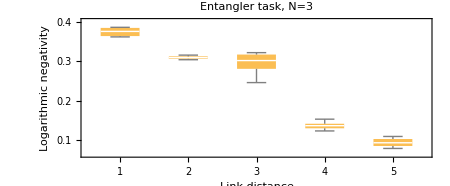

```mathematica
plot=BoxWhiskerChart[listresults,ImageSize->450,LabelStyle->15,FrameLabel->{"Link distance","Logarithmic negativity"},PlotLabel->"Entangler task, N=3",AspectRatio->1/(1+Sqrt[2]),ChartLabels->listdelay]
```

### Show the result

```mathematica
plot
```

-Graphics-

## 2.3 Panel b: vary both link distance and reservoir size

### Parameters

NB! The actual value of the bare frequency should not change the results.

```mathematica
n=3;
m=1;
ωbare=0.25;
g=1.6ωbare^2;(*gives the familiar 0.1 for bare frequency 0.25*)
Δt=2.Pi/ωbare;
ρlimit=0.99;
r=0.;(*squeeze the inputs before processing?*)
seed=300;
readout=Function[listσ,listσ[[All,2n+1;;,2n+1;;]]];
preprocess=Identity;
```

```mathematica
{prep,train,test}={40,80,40};
```

```mathematica
listdelay=Range[5];
listn=Range[5];
```

### Get the results

```mathematica
listtfixed={2};
listtfixed={2,4,6,8};
```

For this, if we want to sacrifice speed for quality later should include t as input and then cycle through some list of values, at the end choosing the best result.

```mathematica
(*reset the RNG of all parallel kernels*)
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

```mathematica
listinput=ConstantArray[getσthsqz[0.,r,0.,ωbare],{prep+train+test}];
```

```mathematica
re=0;SetSharedVariable[re];(*for keeping track*)
Monitor[
listresults=ParallelTable[
res=Max@Table[
{matH,initσ}=getrandomreservoir[n,ωbare,g];
(*set the time between inputs*)
Δt=tfixed Pi/ωbare;
(*get bona fide initial population*)
initpoints=3 10n m;
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
(*proceed*)
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
readout=Function[listσ,listσ[[All,2n+1;;,2n+1;;]]];(*think the readout is not actually used..*)
res=First@trainertesterentangler[matH,ωbare,initσ,preprocess,listinput,"banaanikotka",readout,Mean[loganega[#]]&,prep,train,test,method,τ,Δt,m,g],{tfixed,listtfixed}];
re=re+1;
res,
{realizations},{n,listn},{τ,listdelay},Method->"FinestGrained"],
ProgressIndicator[re,{0,realizations Length[listdelay]Length[listn]}]];//AbsoluteTiming
```

{3656.78,Null}

```mathematica
(listmedianresults=Map[Median,Transpose[listresults,{3,1,2}],{2}])//MatrixForm
```

(0.30546 | 0.0679964 | 0.0385138 | 0.0271429 | 0.0212282
0.362116 | 0.306505 | 0.124087 | 0.0807843 | 0.0642329
0.365598 | 0.315478 | 0.284926 | 0.137078 | 0.0893658
0.370626 | 0.322056 | 0.303026 | 0.24086 | 0.106686
0.359014 | 0.321467 | 0.296447 | 0.213551 | 0.136818)

```mathematica
(*median was 0.328 with a fixed time at 2*)
(*now much more :) *)
```

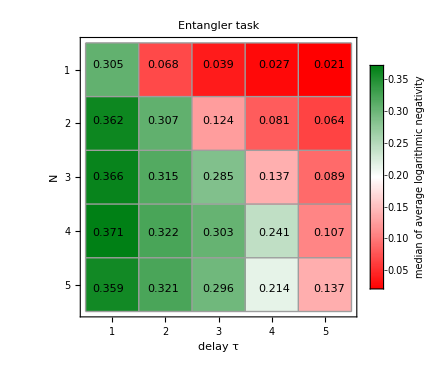

```mathematica
plotmedianresults=ArrayPlot[listmedianresults,ImageSize->375,LabelStyle->15,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Rotate["median of average logarithmic negativity",1.5Pi],Right]],FrameLabel->{"N","delay τ"},ColorFunctionScaling->True,ColorFunction->"RedGreenSplit",PlotLabel->"Entangler task",FrameTicks->{{True,False},{True,False}},Mesh->True,Frame->True,makearraylabels[listmedianresults,0.001,Directive[Black,Medium]]]
```

### Show the result

```mathematica
plotmedianresults
```

-Graphics-

## 2.4 Figure 4

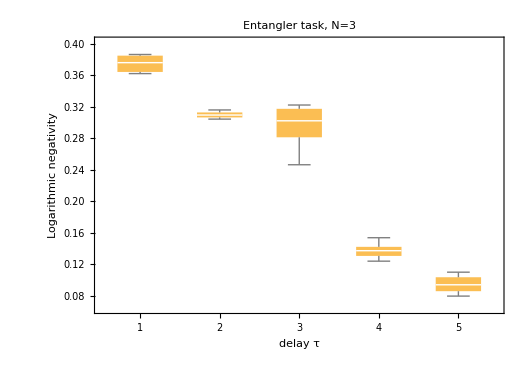
a |  | b
-Graphics- |  | -Graphics-

```mathematica
s=Spacer[30];
plotcombo=Grid[
{{Style["a",20,Bold],"",Style["b",20,Bold]},{Show[plot,ImageSize->525,AspectRatio->1./Sqrt[2],ImagePadding->{{Automatic, 5}, {Automatic, 9}},FrameLabel->{"delay τ","Logarithmic negativity"}],s,Show[plotmedianresults,ImagePadding->{{Automatic, 5}, {Automatic, 11}}]}},Alignment->Left
]
```